# Lab 7 : Polar Curves

## 1. Plot the polar graph r = 1 + Cos [θ].

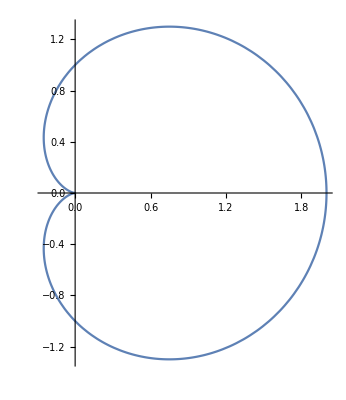

```mathematica
PolarPlot[1+Cos[t],{t,0,2 π}]
```

We used the letter t instead of θ to save some typing time. Your exercise is to plot the following polar curves:
a.  r = -4 Sin [θ]
b.  r = 3( 1 - Cos [θ] )
c.  r = -3 Cos [2θ]
Fill in the functions and domains yourself and then execute. (Use the example above as a guide.) (If you like to use θ  instead of t, you can either copy-paste from above or input it manually by [ESC]theta[ESC] using the escape keys.)

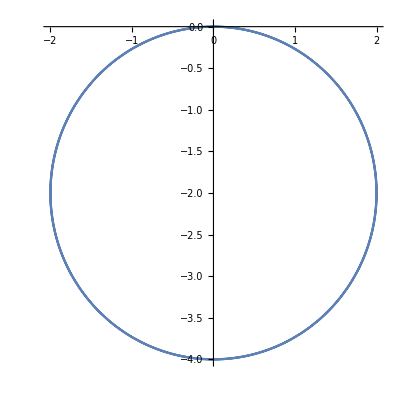

```mathematica
PolarPlot[ -4Sin[t],{t,0 ,2Pi }]
```

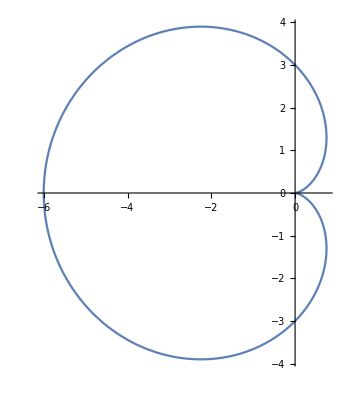

```mathematica
PolarPlot[ 3(1-Cos[t]),{t,0 ,2Pi }]
```

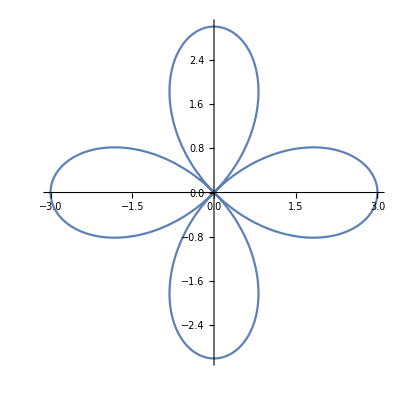

```mathematica
PolarPlot[  -3Cos[2t],{t,0 ,2Pi }]
```

## 2. In this problem, you will be asked to match some reference graphs with their associated polar plots.

```mathematica
twochoices[f1_,f2_,w1_,w2_]:=GraphicsGrid[{{PolarPlot[f1,{th,0,2 π},PlotLabel->w1],PolarPlot[f2,{th,0,2 π},PlotLabel->w2]}}];
tworefs[f1_,f2_,w1_,w2_]:=Print[GraphicsGrid[{{Plot[f1,{th,0,2 π},PlotLabel->w1,Ticks->{{0,π,2 π},Automatic}],Plot[f2,{th,0,2 π},PlotLabel->w2,Ticks->{{0,π,2 π},Automatic}]}}]];
ShowChoices2:=Module[{f1,f2,f3,f4,f5,f6},f1=Abs[Sin[th]];f2=1+Sin[th];f5=1-Sin[th];f6=Sin[th];f3=(Abs[th-π] 2)/π;f4=2-f3;Print[twochoices[f1,f2,"Choice A","Choice B"]];Print[twochoices[f3,f4,"Choice C","Choice D"]];Print[twochoices[f5,f6,"Choice E","Choice F"]];];
ShowReferences2:=Module[{f1,f2,f3,f4},f1=1-Sin[th];f2=Sin[th];f3=(Abs[th-π] 2)/π;f4=2-f3;tworefs[f1,f2,"Reference #1","Reference #2"];tworefs[f3,f4,"Reference #3","Reference #4"];];
```

Execute the following command to get a list of polar plots.

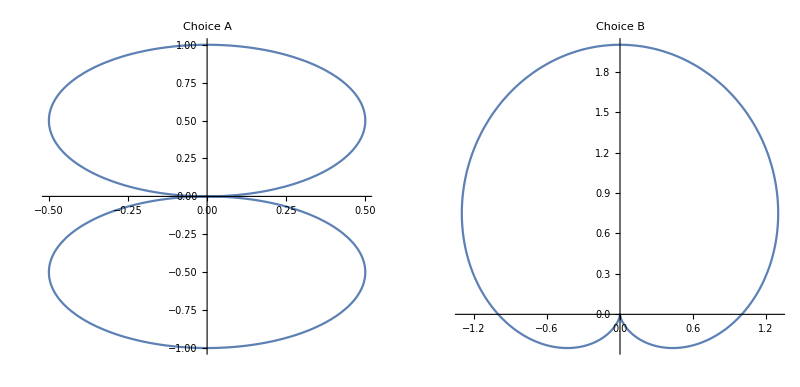

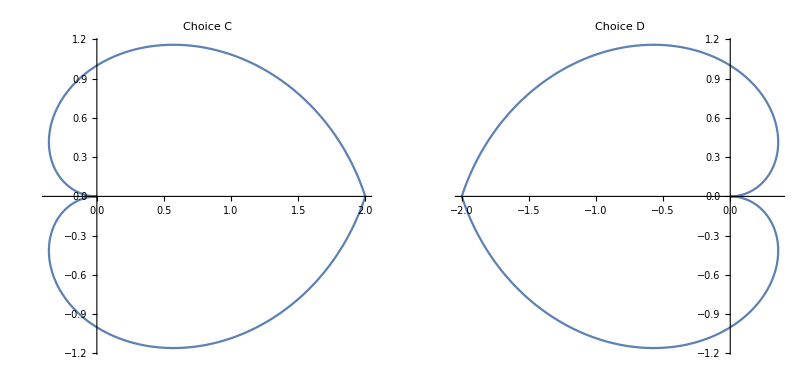

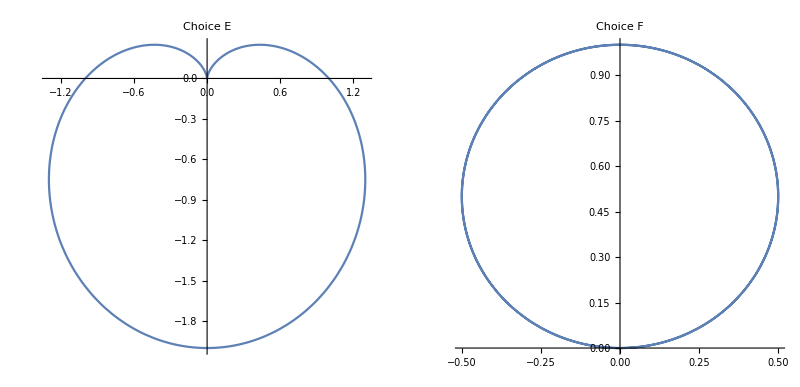

```mathematica
ShowChoices2
```

Then execute the following command to get a list of reference graphs of r vs θ in cartesian coordinates.

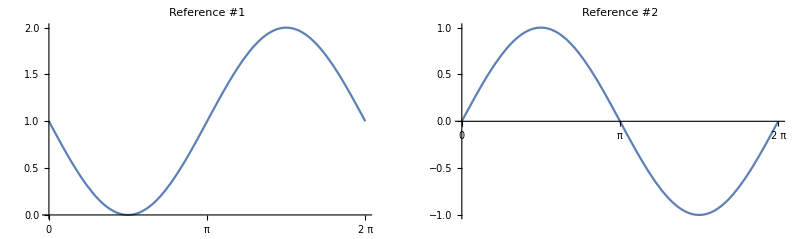

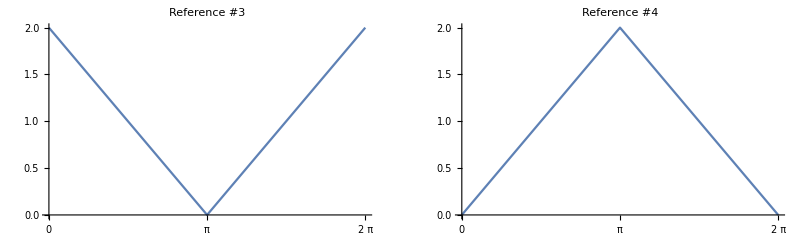

```mathematica
ShowReferences2
```

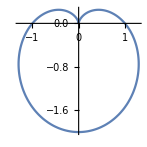

```mathematica
PolarPlot[ 1-Sin[t],{t,0 ,2Pi }]
```

#### Reference Graph 1 matches to Choice ... E

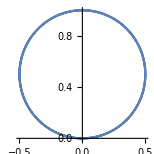

```mathematica
PolarPlot[ Sin[t],{t,0 ,2Pi }]
```

#### Reference Graph 2 matches to Choice ... F

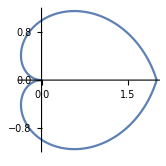

```mathematica
PolarPlot[Abs[2(1-t/Pi)],{t,0 ,2Pi }]
```

#### Reference Graph 3 matches to Choice ... C

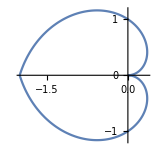

```mathematica
PolarPlot[2-Abs[2(1-t/Pi)],{t,0 ,2Pi }]
```

#### Reference Graph 4 matches to Choice ... D

## 3. Consider the polar equation r=sin^3 θ. Plot it.

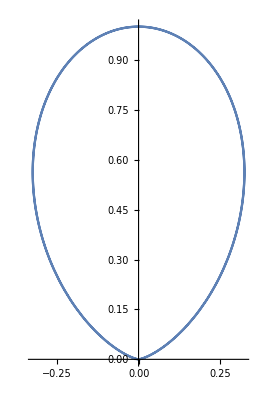

```mathematica
PolarPlot[Sin[θ]^3,{θ,0,2 π}]
```

Convert the polar equation  r=sin^3 θ  to a Cartesian equation involving only x and y. (Hint: Mulitply both sides of the equation by r^3. Remember, x = r  cos θ, y = r  sin θ, r=√(x^2+y^2).) You might have to work this out on scrap paper.

#### Response:r^4= (r sin (θ))^3⇒ (x^2+y^2)^2= y^3

To make sure your Cartesian equation is correct, we can plot it implicitly (that is, without solving for y). Fill in your Cartesian equation below. (Note that the double equal signs == is on purpose.)

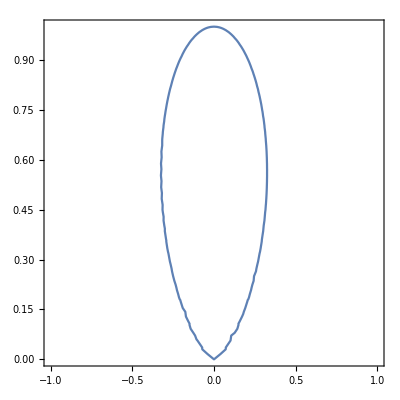

```mathematica
ContourPlot[   (x^2+y^2)^2==y^3 , {x, -1, 1},{y,0,1}]
```

Does this look like the polar plot?

#### Response: Yes. With different scaling on the axes.